```mathematica
IntegerDigits[]
```

```mathematica
T=Table[1,{i,1,28}];
N[8 FromDigits[T,2]/(1024 1024 1024)]
```

2.

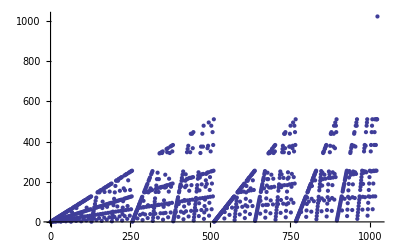

```mathematica
LS=2;
n=10;nP=LS^n;
pU=Table[0,{i,1,nP}];
L2D={};
For[P=0,P<nP,P++,
sP = P;mP=P;
(*Print["Shifts: "];*)
For[i=0,i<n,i++,
(*Print[IntegerDigits[sP,LS,n]];*)
nsP=Quotient[sP,LS] + Mod[sP,LS] LS^(n-1);
sP=nsP;
mP=Min[mP,sP];
];
AppendTo[L2D,{P,mP}];
(*Print["P = ",P," or ",IntegerDigits[P,LS,n],", mP = ",mP," or ",IntegerDigits[mP,LS,n]];*)
];
ListPlot[L2D,PlotRange->All]
```